# Fits to Brody distribution, and calculations for density of states

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
bins=Table[x,{x,0,5,0.2}];
bFit=Table[0.5*(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}];
Ewindowsize=30.0;
```

## Run1

```mathematica
rundata1=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run1/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
50			100

LobattoPoints		NumChannels	Order
100			100		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
75.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.0d0		1.0d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.25d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff1-Ewindowsize<#<Ecutoff1-1.&;
curvestemp1=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run1/AdiabaticCurves.dat"]];
Curves1=Table[Table[{curvestemp1[[1,i]],curvestemp1[[j,i]]},{i,1,Length[curvestemp1[[1]]]}],{j,2,Length[curvestemp1]}];
Evals1=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run1/Eigenvals.dat"]];
Ecutoff1=Evals1[[4]]
Evals1=Sort[Drop[Evals1,1;;4]];
eValsBound1 = Sort[Select[Evals1,SampleRange]]
```

-181.012

{-210.635,-210.346,-210.304,-210.257,-209.943,-209.682,-209.488,-209.178,-208.774,-208.568,-208.497,-208.462,-208.24,-208.017,-207.54,-206.467,-205.96,-205.92,-205.593,-205.502,-204.923,-204.82,-204.513,-204.182,-204.039,-203.719,-202.101,-201.722,-201.338,-201.122,-201.013,-200.801,-200.555,-200.476,-200.423,-200.157,-200.029,-199.806,-199.567,-199.287,-199.059,-198.301,-197.878,-197.743,-197.619,-197.307,-196.948,-196.852,-196.409,-196.187,-196.034,-195.59,-195.378,-195.033,-194.626,-194.302,-194.007,-193.728,-193.71,-192.979,-192.638,-192.314,-192.283,-191.866,-191.645,-191.557,-191.499,-191.185,-191.077,-191.028,-190.993,-190.566,-190.055,-189.988,-189.975,-189.793,-189.628,-189.264,-188.975,-188.97,-188.54,-188.217,-188.043,-187.74,-187.598,-187.386,-186.907,-186.859,-186.632,-186.321,-186.196,-185.94,-185.736,-185.684,-185.507,-185.052,-184.654,-184.476,-184.311,-184.176,-183.718,-183.603,-183.367,-183.253,-183.228,-183.045,-182.953,-182.708,-182.622,-182.472,-182.368,-182.262,-182.146}

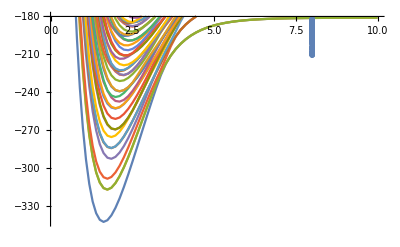

```mathematica
pcurves1=ListPlot[Curves1,PlotMarkers->None,Joined->True,PlotRange->{Min[curvestemp1[[2]]],Ecutoff1+1}];
penergies1=ListPlot[Table[{8,eValsBound1[[i]]},{i,1,Length[eValsBound1]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves1,penergies1]
```

```mathematica
Es1=Table[eValsBound1[[i+1]]-eValsBound1[[i]],{i,1,Length[eValsBound1]-1}];
eTrim1= Select[Es1,#>0.0000001&];
avg1 = Mean[eTrim1];
eTrim1 = eTrim1/avg1;
(*Sort[eTrim1];*)
Length[Es1];
Length[eTrim1];
ρ1=1/avg1;
EspaceBin1=BinCounts[eTrim1,{bins}];
NormBrodyBinCs1=Table[EspaceBin1[[i]]/Total[EspaceBin1]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist1 = Table[{bFit[[i]],NormBrodyBinCs1[[i]]},{i,1,Length[bFit]}]
phist1=ListPlot[brodyPdist1,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars1 = FindFit[brodyPdist1,{PBrody[s,w],w>0,w<1},{w},s]
pfit1=Plot[PBrody[s,w/.pars1],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.540541},{0.3,0.495495},{0.5,0.720721},{0.7,0.405405},{0.9,0.765766},{1.1,0.405405},{1.3,0.630631},{1.5,0.315315},{1.7,0.315315},{1.9,0.18018},{2.1,0.045045},{2.3,0.045045},{2.5,0.},{2.7,0.},{2.9,0.0900901},{3.1,0.},{3.3,0.},{3.5,0.},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.045045},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.47747}

```mathematica
ρ1
```

3.93138

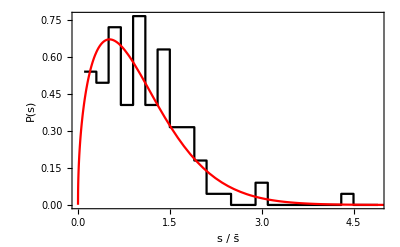

```mathematica
Show[phist1,pfit1,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

## Run2

```mathematica
rundata2=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run2/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
50			100

LobattoPoints		NumChannels	Order
100			100		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
75.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.0d0		1.0d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.25d0		0d0 		0.5d0

Left		Right		Bot		Top
0		1		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff2-Ewindowsize<#<Ecutoff2-1&
curvestemp2=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run2/AdiabaticCurves.dat"]];
Curves2=Table[Table[{curvestemp2[[1,i]],curvestemp2[[j,i]]},{i,1,Length[curvestemp2[[1]]]}],{j,2,Length[curvestemp2]}];
Evals2=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run2/Eigenvals.dat"]];
Ecutoff2=Evals2[[4]]
Evals2=Sort[Drop[Evals2,1;;4]];
eValsBound2 = Sort[Select[Evals2,SampleRange]]
```

Ecutoff2-Ewindowsize<#1<Ecutoff2-1&

-181.012

{-210.679,-210.421,-210.2,-210.156,-210.04,-210.01,-209.882,-209.673,-209.298,-208.835,-208.674,-208.502,-208.421,-208.202,-207.73,-207.727,-206.529,-206.485,-206.131,-205.811,-205.6,-205.475,-205.091,-204.656,-204.5,-204.456,-204.143,-203.931,-203.805,-203.354,-201.828,-201.373,-201.33,-201.134,-200.886,-200.813,-200.706,-200.609,-200.398,-200.369,-200.264,-200.117,-200.017,-199.895,-199.633,-199.439,-199.181,-198.806,-198.714,-198.584,-198.308,-197.696,-197.669,-197.553,-197.398,-197.357,-197.023,-196.751,-196.415,-196.092,-196.009,-195.793,-195.365,-195.08,-194.837,-194.154,-193.787,-193.191,-192.944,-192.785,-192.582,-192.395,-192.21,-192.084,-192.027,-191.718,-191.608,-191.477,-191.398,-191.285,-191.119,-190.885,-190.871,-190.665,-190.621,-190.351,-189.826,-189.633,-189.515,-189.105,-188.842,-188.777,-188.359,-188.132,-187.926,-187.818,-187.761,-187.481,-187.441,-187.246,-187.09,-186.979,-186.824,-186.656,-186.651,-186.417,-186.35,-185.755,-185.338,-185.282,-185.121,-184.7,-184.69,-184.454,-184.27,-184.226,-184.059,-183.725,-183.708,-183.505,-183.011,-182.946,-182.744,-182.67,-182.652,-182.521,-182.169}

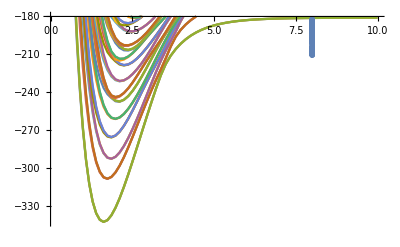

```mathematica
pcurves2=ListPlot[Curves2,PlotMarkers->None,Joined->True,PlotRange->{Min[curvestemp2[[2]]],Ecutoff2+1}];
penergies2=ListPlot[Table[{8,eValsBound2[[i]]},{i,1,Length[eValsBound2]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves2,penergies2]
```

```mathematica
Es2=Table[eValsBound2[[i+1]]-eValsBound2[[i]],{i,1,Length[eValsBound2]-1}];
eTrim2 = Select[Es2,#>0.0000001&];
avg2 = Mean[eTrim2];
eTrim2 = eTrim2/avg2;
(*Sort[eTrim2];*)
Length[Es2];
Length[eTrim2];
ρ2=1/avg2;
EspaceBin2=BinCounts[eTrim2,{bins}];
NormBrodyBinCs2=Table[EspaceBin2[[i]]/Total[EspaceBin2]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist2 = Table[{bFit[[i]],NormBrodyBinCs2[[i]]},{i,1,Length[bFit]}]
phist2=ListPlot[brodyPdist2,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars2 = FindFit[brodyPdist2,{PBrody[s,w],w>0,w<1},{w},s]
pfit2=Plot[PBrody[s,w/.pars2],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.685484},{0.3,0.443548},{0.5,0.806452},{0.7,0.483871},{0.9,0.766129},{1.1,0.483871},{1.3,0.241935},{1.5,0.282258},{1.7,0.16129},{1.9,0.282258},{2.1,0.16129},{2.3,0.0403226},{2.5,0.},{2.7,0.120968},{2.9,0.},{3.1,0.0403226},{3.3,0.},{3.5,0.},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.307044}

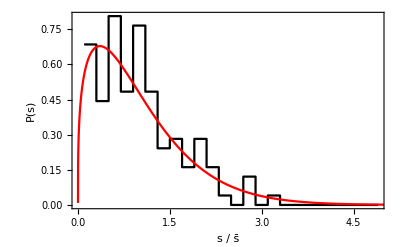

```mathematica
Show[phist2,pfit2,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

## Run3

```mathematica
rundata3=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run3/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
100			100

LobattoPoints		NumChannels	Order
100			200		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
75.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.0d0		1.0d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.5d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff3-Ewindowsize<#<Ecutoff3-1&
curvestemp3=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run3/AdiabaticCurves.dat"]];
Curves3=Table[Table[{curvestemp3[[1,i]],curvestemp3[[j,i]]},{i,1,Length[curvestemp3[[1]]]}],{j,2,Length[curvestemp3]}];
Evals3=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run3/Eigenvals.dat"]];
Ecutoff3=Evals3[[4]]
Evals3=Sort[Drop[Evals3,1;;4]];
eValsBound3 = Sort[Select[Evals3,SampleRange]]
```

Ecutoff3-Ewindowsize<#1<Ecutoff3-1&

-181.012

{-210.679,-210.635,-210.421,-210.346,-210.304,-210.257,-210.2,-210.156,-210.04,-210.01,-209.943,-209.882,-209.682,-209.673,-209.488,-209.298,-209.178,-208.835,-208.774,-208.674,-208.568,-208.502,-208.497,-208.462,-208.421,-208.24,-208.202,-208.017,-207.73,-207.727,-207.54,-206.529,-206.485,-206.467,-206.131,-205.96,-205.92,-205.811,-205.6,-205.593,-205.502,-205.475,-205.091,-204.923,-204.82,-204.656,-204.513,-204.5,-204.456,-204.182,-204.143,-204.039,-203.931,-203.805,-203.719,-203.354,-202.101,-201.828,-201.722,-201.373,-201.338,-201.33,-201.134,-201.122,-201.013,-200.886,-200.813,-200.801,-200.706,-200.609,-200.555,-200.476,-200.423,-200.398,-200.369,-200.264,-200.157,-200.117,-200.029,-200.017,-199.895,-199.806,-199.633,-199.567,-199.439,-199.287,-199.181,-199.059,-198.806,-198.714,-198.584,-198.308,-198.301,-197.878,-197.743,-197.696,-197.669,-197.619,-197.553,-197.398,-197.357,-197.307,-197.023,-196.948,-196.852,-196.751,-196.415,-196.409,-196.187,-196.092,-196.034,-196.009,-195.793,-195.59,-195.378,-195.365,-195.08,-195.033,-194.837,-194.626,-194.302,-194.154,-194.007,-193.787,-193.728,-193.71,-193.191,-192.979,-192.944,-192.785,-192.638,-192.582,-192.395,-192.314,-192.283,-192.21,-192.084,-192.027,-191.866,-191.718,-191.645,-191.608,-191.557,-191.499,-191.477,-191.398,-191.285,-191.185,-191.119,-191.077,-191.028,-190.993,-190.885,-190.871,-190.665,-190.621,-190.566,-190.351,-190.055,-189.988,-189.975,-189.826,-189.793,-189.633,-189.628,-189.515,-189.264,-189.105,-188.975,-188.97,-188.842,-188.777,-188.539,-188.359,-188.217,-188.132,-188.043,-187.926,-187.818,-187.761,-187.74,-187.598,-187.481,-187.441,-187.386,-187.246,-187.091,-186.979,-186.907,-186.859,-186.824,-186.656,-186.651,-186.632,-186.417,-186.35,-186.321,-186.196,-185.94,-185.755,-185.736,-185.684,-185.507,-185.338,-185.282,-185.121,-185.052,-184.7,-184.69,-184.654,-184.476,-184.454,-184.311,-184.27,-184.226,-184.176,-184.059,-183.725,-183.718,-183.709,-183.603,-183.505,-183.367,-183.253,-183.228,-183.045,-183.011,-182.953,-182.946,-182.744,-182.708,-182.67,-182.652,-182.622,-182.521,-182.472,-182.368,-182.262,-182.169,-182.146}

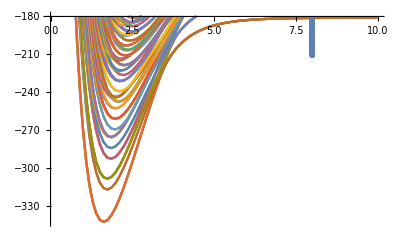

```mathematica
pcurves3=ListPlot[Curves3,Joined->True,PlotRange->{Min[curvestemp3[[2]]],Ecutoff3+1}];
penergies3=ListPlot[Table[{8,eValsBound3[[i]]},{i,1,Length[eValsBound3]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves3,penergies3]
```

```mathematica
Es3=Table[eValsBound3[[i+1]]-eValsBound3[[i]],{i,1,Length[eValsBound3]-1}];
eTrim3 = Select[Es3,#>0.0000001&];
avg3 = Mean[eTrim3];
eTrim3 = eTrim3/avg3;
Sort[eTrim3];
Length[Es3];
Length[eTrim3];
ρ3=1/avg3;
EspaceBin3=BinCounts[eTrim3,{bins}];
NormBrodyBinCs3=Table[EspaceBin3[[i]]/Total[EspaceBin3]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist3 = Table[{bFit[[i]],NormBrodyBinCs3[[i]]},{i,1,Length[bFit]}]
phist3=ListPlot[brodyPdist3,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->{Blue}];
pars3 = FindFit[brodyPdist3,{PBrody[s,w],w>0,w<1},{w},s]
pfit3=Plot[PBrody[s,w/.pars3],{s,0,5},PlotRange->All,PlotStyle->{Green}];
```

{{0.1,0.632911},{0.3,0.843882},{0.5,0.696203},{0.7,0.379747},{0.9,0.632911},{1.1,0.379747},{1.3,0.295359},{1.5,0.337553},{1.7,0.253165},{1.9,0.105485},{2.1,0.0632911},{2.3,0.105485},{2.5,0.0421941},{2.7,0.0421941},{2.9,0.105485},{3.1,0.021097},{3.3,0.021097},{3.5,0.021097},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.021097},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.198731}

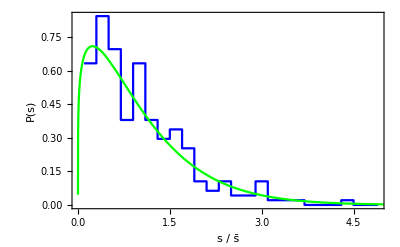

```mathematica
pall3=Show[phist3,pfit3,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

##### Analysis so far

Runs 1 and 2 have taken advantage of a possible symmetry by further reducing the coordinate space.  If my guess is right, then the density of states for run3 should be roughly twice that of run 1 and 2 since I expect both “even and odd” states about phi = π/4 to be present in run 3, but only even states in run1 and odd states in run2

```mathematica
ρ1
ρ2
ρ3
```

3.93138

4.4196

8.37651

```mathematica
ρ1+ρ2
```

8.35099

Further, I expect that if these states (even and odd) do not couple since the Hamiltonian is symmetric about ϕ=π/4, then overlaying these two distributions will result in a distribution similar to that of run3

```mathematica
eValsBoundCombined =Sort[ Flatten[{eValsBound1,eValsBound2}]]
EsCombined=Table[eValsBoundCombined[[i+1]]-eValsBoundCombined[[i]],{i,1,Length[eValsBoundCombined]-1}];
eTrimCombined = Select[EsCombined,#>0.0000001&];
avgCombined = Mean[eTrimCombined];
eTrimCombined = eTrimCombined/avgCombined;
(*Sort[eTrimCombined];*)
Length[eTrimCombined];
ρCombined=1/avgCombined;
EspaceBinCombined=BinCounts[eTrimCombined,{bins}];
NormBrodyBinCsCombined=Table[EspaceBinCombined[[i]]/Total[EspaceBinCombined]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdistCombined = Table[{bFit[[i]],NormBrodyBinCsCombined[[i]]},{i,1,Length[bFit]}]
phistCombined=ListPlot[brodyPdistCombined,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->{Black,Dashed}];
parsCombined = FindFit[brodyPdistCombined,{PBrody[s,w],w>0,w<1},{w},s]
pfitCombined=Plot[PBrody[s,w/.parsCombined],{s,0,5},PlotRange->All,PlotStyle->{Red,Dashed}];
```

{-210.679,-210.635,-210.421,-210.346,-210.304,-210.257,-210.2,-210.156,-210.04,-210.01,-209.943,-209.882,-209.682,-209.673,-209.488,-209.298,-209.178,-208.835,-208.774,-208.674,-208.568,-208.502,-208.497,-208.462,-208.421,-208.24,-208.202,-208.017,-207.73,-207.727,-207.54,-206.529,-206.485,-206.467,-206.131,-205.96,-205.92,-205.811,-205.6,-205.593,-205.502,-205.475,-205.091,-204.923,-204.82,-204.656,-204.513,-204.5,-204.456,-204.182,-204.143,-204.039,-203.931,-203.805,-203.719,-203.354,-202.101,-201.828,-201.722,-201.373,-201.338,-201.33,-201.134,-201.122,-201.013,-200.886,-200.813,-200.801,-200.706,-200.609,-200.555,-200.476,-200.423,-200.398,-200.369,-200.264,-200.157,-200.117,-200.029,-200.017,-199.895,-199.806,-199.633,-199.567,-199.439,-199.287,-199.181,-199.059,-198.806,-198.714,-198.584,-198.308,-198.301,-197.878,-197.743,-197.696,-197.669,-197.619,-197.553,-197.398,-197.357,-197.307,-197.023,-196.948,-196.852,-196.751,-196.415,-196.409,-196.187,-196.092,-196.034,-196.009,-195.793,-195.59,-195.378,-195.365,-195.08,-195.033,-194.837,-194.626,-194.302,-194.154,-194.007,-193.787,-193.728,-193.71,-193.191,-192.979,-192.944,-192.785,-192.638,-192.582,-192.395,-192.314,-192.283,-192.21,-192.084,-192.027,-191.866,-191.718,-191.645,-191.608,-191.557,-191.499,-191.477,-191.398,-191.285,-191.185,-191.119,-191.077,-191.028,-190.993,-190.885,-190.871,-190.665,-190.621,-190.566,-190.351,-190.055,-189.988,-189.975,-189.826,-189.793,-189.633,-189.628,-189.515,-189.264,-189.105,-188.975,-188.97,-188.842,-188.777,-188.54,-188.359,-188.217,-188.132,-188.043,-187.926,-187.818,-187.761,-187.74,-187.598,-187.481,-187.441,-187.386,-187.246,-187.09,-186.979,-186.907,-186.859,-186.824,-186.656,-186.651,-186.632,-186.417,-186.35,-186.321,-186.196,-185.94,-185.755,-185.736,-185.684,-185.507,-185.338,-185.282,-185.121,-185.052,-184.7,-184.69,-184.654,-184.476,-184.454,-184.311,-184.27,-184.226,-184.176,-184.059,-183.725,-183.718,-183.708,-183.603,-183.505,-183.367,-183.253,-183.228,-183.045,-183.011,-182.953,-182.946,-182.744,-182.708,-182.67,-182.652,-182.622,-182.521,-182.472,-182.368,-182.262,-182.169,-182.146}

{{0.1,0.632911},{0.3,0.843882},{0.5,0.696203},{0.7,0.379747},{0.9,0.632911},{1.1,0.379747},{1.3,0.295359},{1.5,0.337553},{1.7,0.253165},{1.9,0.105485},{2.1,0.0632911},{2.3,0.105485},{2.5,0.0421941},{2.7,0.0421941},{2.9,0.105485},{3.1,0.021097},{3.3,0.021097},{3.5,0.021097},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.021097},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.198731}

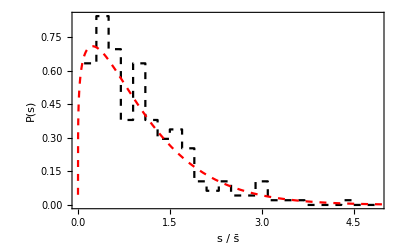

```mathematica
pcomb=Show[phistCombined,pfitCombined,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

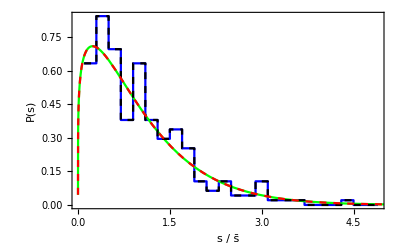

```mathematica
Show[pall3,pcomb]
```

## Run4

```mathematica
rundata4=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run4/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
100			100

LobattoPoints		NumChannels	Order
120			200		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
75.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.5d0		1.5d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.5d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff4-Ewindowsize<#<Ecutoff4-1&
curvestemp4=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run4/AdiabaticCurves.dat"]];
Curves4=Table[Table[{curvestemp4[[1,i]],curvestemp4[[j,i]]},{i,1,Length[curvestemp4[[1]]]}],{j,2,Length[curvestemp4]}];
Evals4=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs75/run4/Eigenvals.dat"]];
Ecutoff4=Evals4[[4]]
Evals4=Sort[Drop[Evals4,1;;4]];
eValsBound4 = Sort[Select[Evals4,SampleRange]]
```

Ecutoff4-Ewindowsize<#1<Ecutoff4-1&

-183.703

{-213.679,-213.347,-213.305,-213.276,-213.153,-212.803,-212.726,-212.587,-212.499,-212.373,-212.146,-212.088,-212.024,-212.007,-211.952,-211.825,-211.642,-211.486,-211.421,-211.357,-211.11,-211.006,-210.858,-210.729,-210.672,-210.554,-210.468,-210.232,-210.084,-210.009,-209.565,-209.459,-209.37,-209.092,-209.013,-208.89,-208.845,-208.748,-208.667,-208.471,-208.419,-208.401,-208.255,-207.953,-207.914,-207.882,-207.61,-207.36,-207.271,-206.854,-206.668,-206.542,-206.334,-206.295,-206.227,-206.174,-206.088,-205.979,-205.92,-205.879,-205.842,-205.773,-205.724,-205.638,-205.568,-205.486,-205.427,-205.338,-205.273,-205.158,-205.084,-204.999,-204.666,-204.613,-204.505,-204.286,-204.256,-204.208,-204.106,-204.02,-203.982,-203.921,-203.833,-203.667,-203.605,-203.509,-203.402,-203.282,-203.22,-203.179,-203.009,-202.874,-202.685,-202.57,-202.353,-202.21,-202.062,-202.016,-201.939,-201.802,-201.697,-201.529,-201.233,-201.149,-201.109,-200.953,-200.908,-200.759,-200.686,-200.507,-200.372,-200.322,-200.198,-200.161,-200.096,-200.077,-199.921,-199.836,-199.653,-199.482,-199.443,-199.42,-199.368,-199.143,-199.058,-198.985,-198.845,-198.483,-198.37,-198.267,-198.195,-198.039,-198.017,-197.912,-197.868,-197.755,-197.6,-197.584,-197.561,-197.47,-197.377,-197.131,-197.082,-197.022,-196.899,-196.875,-196.795,-196.752,-196.729,-196.661,-196.622,-196.581,-196.548,-196.408,-196.278,-196.24,-196.133,-196.046,-195.996,-195.851,-195.773,-195.621,-195.509,-195.486,-195.379,-195.259,-195.218,-195.111,-194.978,-194.766,-194.708,-194.655,-194.527,-194.471,-194.33,-194.267,-194.233,-194.16,-194.05,-194.012,-193.936,-193.87,-193.696,-193.644,-193.592,-193.471,-193.411,-193.267,-193.247,-193.158,-193.104,-193.068,-192.998,-192.929,-192.877,-192.798,-192.729,-192.495,-192.333,-192.238,-192.193,-192.062,-192.039,-191.951,-191.653,-191.517,-191.477,-191.322,-191.297,-191.262,-191.223,-190.973,-190.939,-190.878,-190.795,-190.529,-190.471,-190.462,-190.349,-190.205,-190.162,-190.056,-190.009,-189.95,-189.852,-189.831,-189.822,-189.796,-189.722,-189.666,-189.621,-189.399,-189.378,-189.215,-189.182,-189.075,-189.015,-188.902,-188.824,-188.75,-188.696,-188.639,-188.545,-188.477,-188.414,-188.396,-188.315,-188.272,-188.161,-188.003,-187.835,-187.748,-187.674,-187.599,-187.55,-187.499,-187.451,-187.392,-187.331,-187.239,-187.142,-187.039,-186.923,-186.89,-186.797,-186.745,-186.659,-186.634,-186.611,-186.557,-186.526,-186.474,-186.381,-186.348,-186.271,-186.261,-186.202,-186.062,-186.032,-185.937,-185.897,-185.844,-185.751,-185.69,-185.658,-185.603,-185.58,-185.506,-185.456,-185.333,-185.263,-185.166,-185.019,-184.923,-184.854,-184.791}

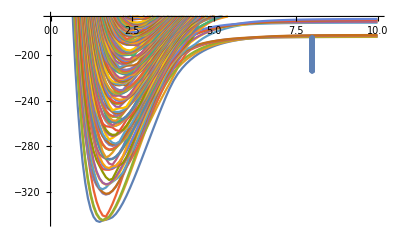

```mathematica
pcurves4=ListPlot[Curves4,Joined->True,PlotRange->{Min[curvestemp4[[2]]],Ecutoff4+18}];
penergies4=ListPlot[Table[{8,eValsBound4[[i]]},{i,1,Length[eValsBound4]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves4,penergies4]
```

```mathematica
Es4=Table[eValsBound4[[i+1]]-eValsBound4[[i]],{i,1,Length[eValsBound4]-1}];
eTrim4 = Select[Es4,#>0.0000001&];
avg4 = Mean[eTrim4];
eTrim4 = eTrim4/avg4;
Sort[eTrim4];
Length[Es4];
Length[eTrim4];
ρ4=1/avg4;
EspaceBin4=BinCounts[eTrim4,{bins}];
NormBrodyBinCs4=Table[EspaceBin4[[i]]/Total[EspaceBin4]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist4 = Table[{bFit[[i]],NormBrodyBinCs4[[i]]},{i,1,Length[bFit]}]
phist4=ListPlot[brodyPdist4,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars4 = FindFit[brodyPdist4,{PBrody[s,w],w>0,w<1},{w},s]
pfit4=Plot[PBrody[s,w/.pars4],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.135593},{0.3,0.644068},{0.5,0.881356},{0.7,0.813559},{0.9,0.677966},{1.1,0.440678},{1.3,0.355932},{1.5,0.372881},{1.7,0.152542},{1.9,0.0847458},{2.1,0.0508475},{2.3,0.101695},{2.5,0.0847458},{2.7,0.0338983},{2.9,0.0169492},{3.1,0.0508475},{3.3,0.0169492},{3.5,0.0338983},{3.7,0.0169492},{3.9,0.},{4.1,0.},{4.3,0.0169492},{4.5,0.0169492},{4.7,0.},{4.9,0.}}

{w→0.679804}

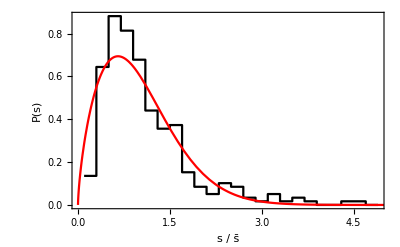

```mathematica
pall4=Show[phist4,pfit4,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

```mathematica
ρ4
```

10.2119

## We need to more closely examine the identical particle symmetries and any other symmetries in the Hamiltonian in order to understand these spectra.

We defined the Jacobi coordinates in the H-tree above so that:

(y⃗)^(12)=S_12 x⃗

where:

1/(√μ)(√μ_12 | -√μ_12 | 0 | 0
0 | 0 | √μ_34 | -√μ_34
(√(μ_(12,34))m_1)/(m_1+m_2) | (√(μ_(12,34))m_2)/(m_1+m_2) | -(√(μ_(12,34))m_3)/(m_3+m_4) | -(√(μ_(12,34))m_4)/(m_3+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))

To keep things as general as possible I’ll assume for now that only particle 1 is of different mass and let m_2=m_3=m_4=m, and m_1=γ m  Then

μ_12=(γ m m)/(γ m+m)=mγ/(1+γ) ⟶ m/2

μ_34=m/2

μ_(12,34)=((γ m+m)(2m))/(3m+γ m)=2m(1+γ)/(3+γ)⟶ m

μ=((γ m m m m)/(γ m+3m))^(1/3)=(m(γ/(3+γ)))^(1/3) ⟶ (m/2^(2/3))

So for the equal-mass case:

2^(1/3)/(√m)(√(m/2) | -√(m/2) | 0 | 0
0 | 0 | √(m/2) | -√(m/2)
(√m)/2 | (√m)/2 | -(√m)/2 | -(√m)/2
m/(√(4m)) | m/(√(4m)) | m/(√(4m)) | m/(√(4m)))=2^(1/3)(√(1/2) | -√(1/2) | 0 | 0
0 | 0 | √(1/2) | -√(1/2)
1/2 | 1/2 | -1/2 | -1/2
1/2 | 1/2 | 1/2 | 1/2)

and

x⃗=S_12^-1(y⃗)^(12)

Then

(y⃗)^(13)=S_13 x⃗=S_13 S_12^-1(y⃗)^(12)

Now note that we could use the same matrix S_12 to construct (y⃗)^(13) if the matrix were to act on a column vector (x_1
x_3
x_2
x_4)  instead of the usual vector x⃗= (x_1
x_2
x_3
x_4).  We can then say:

(x_1
x_3
x_2
x_4) =(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)(x_1
x_2
x_3
x_4)=P_23 x⃗

Hence:

S_13=S_12 P_23

and

(y⃗)^(13)=S_13 x⃗=S_13 S_12^-1(y⃗)^(12)=S_12 P_23 S_12^-1(y⃗)^(12)

Similarly,

(y⃗)^(14)=S_14 x⃗=S_14 S_12^-1(y⃗)^(12)=S_12 P_24 S_12^-1(y⃗)^(12)

where

P_24=(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
S12=2^(1/3)({{√(1/2), -√(1/2), 0, 0}, {0, 0, √(1/2), -√(1/2)}, {1/2, 1/2, -1/2, -1/2}, {1/2, 1/2, 1/2, 1/2}});
```

```mathematica
P24=({{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}});P23=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});P34=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});P14=({{0, 0, 0, 1}, {0, 1, 0, 0}, {0, 0, 1, 0}, {1, 0, 0, 0}});P13=({{0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}});P12=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

```mathematica
𝒫12=Simplify[S12.P12.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫12]
```

(-1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
𝒫34=Simplify[S12.P34.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫34]
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

```mathematica
𝒫14=Simplify[S12.P14.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫14]
```

(1/2 | -1/2 | -1/(√2)
-1/2 | 1/2 | -1/(√2)
-1/(√2) | -1/(√2) | 0)

```mathematica
𝒫13=Simplify[S12.P13.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫13]
```

(1/2 | 1/2 | -1/(√2)
1/2 | 1/2 | 1/(√2)
-1/(√2) | 1/(√2) | 0)

```mathematica
𝒫23=Simplify[S12.P23.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫23]
```

(1/2 | -1/2 | 1/(√2)
-1/2 | 1/2 | 1/(√2)
1/(√2) | 1/(√2) | 0)

```mathematica
𝒫24=Simplify[S12.P24.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫24]
```

(1/2 | 1/2 | 1/(√2)
1/2 | 1/2 | -1/(√2)
1/(√2) | -1/(√2) | 0)

```mathematica
TraditionalForm[FullSimplify[𝒫23.𝒫14]]
```

(0 | -1 | 0
-1 | 0 | 0
0 | 0 | -1)

```mathematica
TraditionalForm[FullSimplify[𝒫24.𝒫13]]
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | -1)

```mathematica
TraditionalForm[FullSimplify[𝒫23.𝒫14.𝒫24.𝒫13]]
```

(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

X_cm=(m_1 x_1+m_2 x_2+m_3 x_3+m_4 x_4)/(m_1+m_2+m_3+m_4)

ρ_1^(12)=x_1-x_2

ρ_2^(12)=x_3-x_4

ρ_3^(12)=(m_1 x_1+m_2 x_2)/(m_1+m_2)-(m_3 x_3+m_4 x_4)/(m_3+m_4)

and mass-scaled Jacobi coordinates as:

y_1^(12)=√(μ_12/μ)(x_1-x_2)

y_2^(12)=√(μ_34/μ)(x_3-x_4)

y_3^(12)=√((μ_(12,34))/μ)((m_1 x_1+m_2 x_2)/(m_1+m_2)-(m_3 x_3+m_4 x_4)/(m_3+m_4))

y_4^(12)=√(M/μ)X_cm

The convention here is that the superscript (12) indicates this coordinate system is convenient for treating the interaction between particles 1 and 2.  In matrix notation:

(y_1^(12)
y_2^(12)
y_3^(12)
y_4^(12))=1/(√μ)(√μ_12 | -√μ_12 | 0 | 0
0 | 0 | √μ_34 | -√μ_34
(√(μ_(12,34))m_1)/(m_1+m_2) | (√(μ_(12,34))m_2)/(m_1+m_2) | -(√(μ_(12,34))m_3)/(m_3+m_4) | -(√(μ_(12,34))m_4)/(m_3+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))(x_1
x_2
x_3
x_4)

Now we define the hyperspherical coordinates as:

y_1^(12)=cos θ_12

y_2^(12)=sin θ_12 cos ϕ_12

y_3^(12)=sin θ_12 sin ϕ_12

```mathematica
Clear[μ4]
```

```mathematica
μ4=(μ12 μ34 μ1234)^(1/3)/.{μ12->((m1 m2)/(m1+m2)),μ34->((m3 m4)/(m3+m4)),μ1234->(((m1+m2)(m3+m4))/(m1+m2+m3+m4)),M->m1+m2+m3+m4}
```

((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/3)

```mathematica
A=1/(√μ4)({{√μ12, -√μ12, 0, 0}, {0, 0, √μ34, -√μ34}, {(√μ1234 m1)/(m1+m2), (√μ1234 m2)/(m1+m2), -(√μ1234 m3)/(m3+m4), -(√μ1234 m4)/(m3+m4)}, {m1/(√M), m2/(√M), m3/(√M), m4/(√M)}})/.{μ12->((m1 m2)/(m1+m2)),μ34->((m3 m4)/(m3+m4)),μ1234->(((m1+m2)(m3+m4))/(m1+m2+m3+m4)),M->m1+m2+m3+m4}//FullSimplify
```

{{(√((m1 m2)/(m1+m2)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),-(√((m1 m2)/(m1+m2)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),0,0},{0,0,(√((m3 m4)/(m3+m4)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),-(√((m3 m4)/(m3+m4)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)},{(m1 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),(m2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),-(m3 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),-(m4 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6))},{m1/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m2/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m3/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m4/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4))}}

Let’s just treat the equal mass case here...

```mathematica
({{x1}, {x2}, {x3}, {x4}})=FullSimplify[Inverse[A].({{x}, {y}, {z}, {XCM}})/.{m1->m,m2->m,m3->β m,m4->β m}];
```

```mathematica
Clear[R]
```

```mathematica
x12=Simplify[x1-x2];FullSimplify[x12,{m>0,β>0}]
x12hyp=Simplify[x12,m>0]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x12hyp,m>0]
```

(2^(1/3) x β^(1/3))/(1+β)^(1/6)

2^(1/3) R (β^2/(1+β))^(1/6) Cos[ϕ] Sin[θ]

```mathematica
x13=FullSimplify[x1-x3,{m>0,β>0}]
x13hyp=Simplify[x13]/.{x->R Sin[θ]Cos[ϕ],y-> R Sin[θ]Sin[ϕ],z-> R Cos[θ]};FullSimplify[x13hyp,{m>0,β>0}]
```

(√m x β-y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (√m β Cos[ϕ]-√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x14=FullSimplify[x1-x4,{m>0,β>0}]
x14hyp=Simplify[x14]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x14hyp,{m>0,β>0}]
```

(√m x β+y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x23=Simplify[x2-x3,{m>0,β>0}]
x23hyp=Simplify[x23]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x23hyp,{m>0,β>0}]
```

-(√m x β+y √(m β)-z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]-Sin[θ] (√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x24=Simplify[x2-x4,{m>0,β>0}]
x24hyp=Simplify[x24]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x24hyp,{m>0,β>0}]
```

(-√m x β+y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (-√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x34=Simplify[x3-x4,{m>0,β>0}]
x34hyp=Simplify[x3-x4,{m>0,β>0}]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x34hyp,{m>0,β>0}]
```

(2^(1/3) y)/(β (1+β))^(1/6)

(2^(1/3) R Sin[θ] Sin[ϕ])/(β (1+β))^(1/6)

```mathematica
Clear[unequalmassxij]
```

```mathematica
unequalmassxij[R_,β_]=FullSimplify[{x12hyp,x13hyp,x14hyp,x23hyp,x24hyp,x34hyp}/.{m->1,θ->t π,ϕ->f π}]
```

{2^(1/3) R (β^2/(1+β))^(1/6) Cos[f π] Sin[π t],(R (√(β (1+β)) Cos[π t]+β Cos[f π] Sin[π t]-√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]+β Cos[f π] Sin[π t]+√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]-√β (√β Cos[f π]+Sin[f π]) Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]-β Cos[f π] Sin[π t]+√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(2^(1/3) R Sin[f π] Sin[π t])/((β+β^2)^(1/6))}

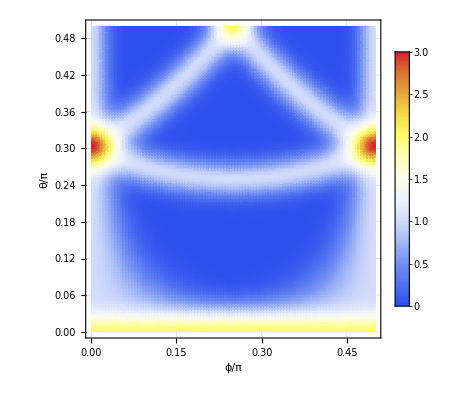

```mathematica
beta=1.0;DensityPlot[Sum[Exp[-(unequalmassxij[10,beta][[i]])^2],{i,1,6}]==0,{f,0.0,.5},{t,0,0.5},GridLines->Automatic,ColorFunction->"TemperatureMap",FrameLabel->{"ϕ/π","θ/π"},PlotPoints->100,PlotLegends->Automatic]
```

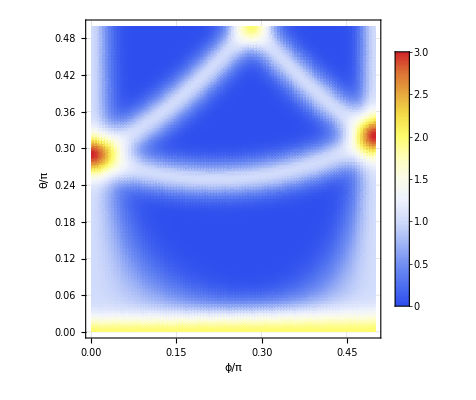

```mathematica
beta=1.5;DensityPlot[Sum[Exp[-(unequalmassxij[10,beta][[i]])^2]/.β->beta,{i,1,6}]==0,{f,0.0,.5},{t,0,0.5},GridLines->Automatic,ColorFunction->"TemperatureMap",FrameLabel->{"ϕ/π","θ/π"},PlotPoints->100,PlotLegends->Automatic]
```

```mathematica
unequalmassxij[[1]]==0
```

5 2^(1/3) (β^2/(1+β))^(1/6) Cos[f π] Sin[π t]==0

```mathematica
c12[β_]:=ContourPlot[Evaluate[unequalmassxij[[1]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Black,FrameLabel->{"ϕ/π","θ/π"}]
c13[β_]:=ContourPlot[Evaluate[unequalmassxij[[2]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Red,FrameLabel->{"ϕ/π","θ/π"}];
c14[β_]:=ContourPlot[Evaluate[unequalmassxij[[3]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Blue,FrameLabel->{"ϕ/π","θ/π"}];
c23[β_]:=ContourPlot[Evaluate[unequalmassxij[[4]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Green,FrameLabel->{"ϕ/π","θ/π"}];
c24[β_]:=ContourPlot[Evaluate[unequalmassxij[[5]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Orange,FrameLabel->{"ϕ/π","θ/π"}];
c34[β_]:=ContourPlot[Evaluate[unequalmassxij[[6]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Yellow,FrameLabel->{"ϕ/π","θ/π"}];
```

```mathematica
c12[1.0]
```

-Graphics-

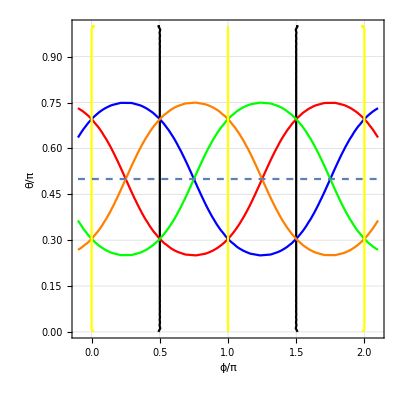

```mathematica
pall=Show[{c12,c13,c14,c23,c24,c34},Plot[0.5,{x,-.1,2.1},PlotStyle->Dashed]]
```

```mathematica
cptable=Table[ContourPlot[Evaluate[unequalmassxij[[i]]==0/.{R->1,α->1}],{f,0,.5},{t,0,.5},GridLines->Automatic,ContourStyle->Black],{i,1,6}];
```

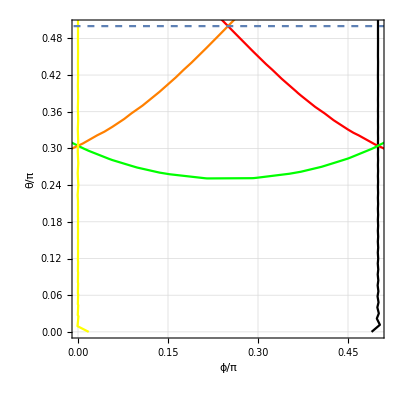

```mathematica
Show[pall,PlotRange->{{0,0.5},{0,0.5}}]
```

### Construct a simpler model with numerical solution

Consider a 3D Hamiltonian of the form

H=ℏ^2/(2μ)∇^2 + 1/2μ r^2+k_xy x y+k_xz x z+k_yz y z

H=ℏ^2/(2μ)∇^2 + 1/2μ r^2+k_xy x y+k_xz x z+k_yz y z

Sakurai, Modern QM page 217 (translated to my preferred notation)

∫ⅆΩ Y_l^(m*)(Ω)Y_l_1^m_1(Ω)Y_l_2^m_2(Ω)=√(((2 l_1+1)(2 l_2+1))/(4π (2l+1)))l_1 0, l_2 0(l_1 l_2) l 0l_1 m_1 l_2 m_2 (l_1 l_2) l m

```mathematica
ME3[l_,m_,l1_,m1_,l2_,m2_]:=√(((2l1+1)(2l2+1))/(4π (2l+1)))ClebschGordan[{l1,0},{l2,0},{l,0}]ClebschGordan[{l1,m1},{l2,m2},{l,m}]
```

So if we need matrix elements of the form:

∫ⅆΩ Y_l^(m*)(Ω)Y_2^m_1(Ω)Y_l_2^m_2(Ω)=√((5(2 l_2+1))/(4π (2l+1)))2,0, l_2,0(l_1 l_2) l 02 m_1 l_2 m_2 (2 l_2) l m

```mathematica
Simplify[ME3[l,m,2,m1,l2,m2]]
```

Piecewise[{{1/(2 (2+l-l2) (l-l2)!)(-1)^(-3 l2+m) (1+2 l) (l^3+l^2 (1+l2)-l (2+2 l2+l2^2)-l2 (2+3 l2+l2^2)) √((5+10 l2)/(π+2 l π)) √(((2+l-l2)!)/((-1+l+l2) (l+l2) (1+l+l2) (2+l+l2) (3+l+l2) (2-l+l2)!)) ThreeJSymbol[{2,m1},{l2,m2},{l,-m}], l∈ℤ&&l2∈ℤ&&l≥0&&l2≥0&&l+l2≥2&&l2≤2+l&&l≤2+l2}, {0, True}}]

Now, since we know

x y = r^2 √(30/π)i (Y_2^-2-Y_2^2)

```mathematica
MExy[R_,l_,m_,l2_,m2_]:=R^2 ⅈ √(30/π)(ME3[l,m,2,-2,l2,m2]-ME3[l,m,2,2,l2,m2])
```

Now the issue is if we want to apply this model to test the two-component 4-fermion problem in 1D, then we need to know how to construct systematically the symmetrized 4-fermion harmonics.  We can specify the subset of harmonics by the boundary conditions implied by identical particle symmetry:

ψ(ϕ=0,θ)=ψ(ϕ=π/2,θ)=0

requires a superposition ψ~Y_l^m-(-1)^m Y_l^-m

```mathematica
Integrate[SphericalHarmonicY[lb,mb,θ,ϕ]SphericalHarmonicY[k,q,θ,ϕ]SphericalHarmonicY[lk,mk,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

∫_0^π ∫_0^(2 π) Sin[θ] SphericalHarmonicY[k,q,θ,ϕ] SphericalHarmonicY[lb,mb,θ,ϕ] SphericalHarmonicY[lk,mk,θ,ϕ]ⅆϕⅆθ